## Customizing Functions

### Overview of Built-In function Properties

Syntax Coloring

```mathematica
Equal[a,b,
```

```mathematica
If[a,b,c,d,e]
```

Optional Arguments

```mathematica
If[False,"true"]
```

```mathematica
If[False,"true","false"]
```

false

```mathematica
If[meh,"true","false","undecided"]
```

undecided

Options

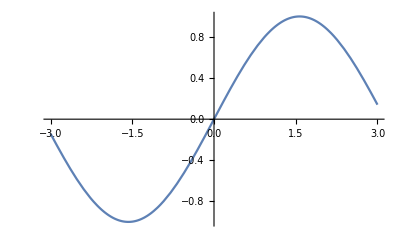

```mathematica
Plot[Sin[x],{x,-3,3}(*,PlotStyle->Red*)]
```

Attributes

```mathematica
Attributes[Manipulate]
```

{HoldAll,Protected,ReadProtected}

Warning/Error Messages

```mathematica
5=x
```

Set::setraw: Cannot assign to raw object 5.

x

### Syntax Coloring

We can create Syntax Coloring properties for functions by using the

```mathematica
ClearAll[f]
SyntaxInformation[f]={"ArgumentsPattern"->{_,_}};
```

```mathematica
f[x]
```

```mathematica
f[x,y,z]
```

### Optional and Default Arguments

```mathematica
myStyle[x_,s_:10,e_:1]:=Framed[Style[x,s^e,Red]]
```

```mathematica
myStyle["Coco Bongo"]
```

Coco Bongo

```mathematica
f[a]/.f[x_+y_]->p[x,y]
```

f[a]

```mathematica
f[a]/.f[x_+y_.]->p[x,y]
```

p[a,0]

### Options

```mathematica
ClearAll[f]
```

```mathematica
?f
```

```mathematica
Options[f]={color->Black}
```

{color→GrayLevel[0]}

```mathematica
?f
```

You can check the options using the Options function

```mathematica
Options[f]
```

{color→GrayLevel[0]}

```mathematica
Options[Manipulate]
```

{Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→None,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}

#### Defining the function with options

```mathematica
f[x_,OptionsPattern[]]:=Module[{a},
a=x^2;
Style[a,OptionValue[color]]
]
```

```mathematica
f[2]
```

4

```mathematica
f[2]
```

4

```mathematica
f[2,color->Red]
```

4

#### Adding Syntax Coloring

```mathematica
ClearAll[f]
Options[f]={color->Red};
SyntaxInformation[f]={"ArgumentsPattern"->{_,OptionsPattern[]}};
```

```mathematica
f[x,color->as,bye->r]
```

```mathematica
Remove[f]
```

#### Warning 1

If color is defined somewhere else this could go wrong

```mathematica
color=7;
f[2,color->Red]
```

f[2,7→RGBColor[1, 0, 0]]

```mathematica
Clear[color]
```

```mathematica
f[2,color->Red]
```

4

#### Warning 2

```mathematica
ClearAll[myPlot]
Options[myPlot]=Join[{minValue->0,maxValue->5},Options[Plot]]
```

{minValue→0,maxValue→5,AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
myPlot[func_,opts:OptionsPattern[]]:=Plot[func,{x,OptionValue[minValue],OptionValue[maxValue]},opts]
```

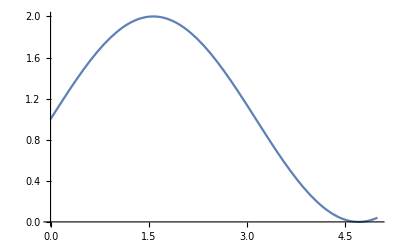

```mathematica
myPlot[Sin[x]+1]
```

```mathematica
myPlot[Sin[x]+1,minValue->0,PlotRange-> 10]
```

Plot::optx: Unknown option minValue→0 in Plot[1+Sin[x],{x,OptionValue[myPlot,{minValue→0,PlotRange→10},minValue],OptionValue[myPlot,{minValue→0,PlotRange→10},maxValue]},minValue→0,PlotRange→10].

Plot[1+Sin[x],{x,OptionValue[myPlot,{minValue→0,PlotRange→10},minValue],OptionValue[myPlot,{minValue→0,PlotRange→10},maxValue]},minValue→0,PlotRange→10]

```mathematica
myPlot[func_,opts:OptionsPattern[]]:=Plot[func,{x,OptionValue[minValue],OptionValue[maxValue]},Evaluate[FilterRules[{opts},Options[Plot]]]]
```

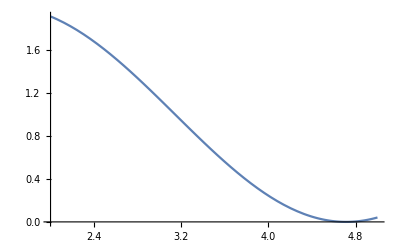

```mathematica
myPlot[Sin[x]+1,minValue->2]
```

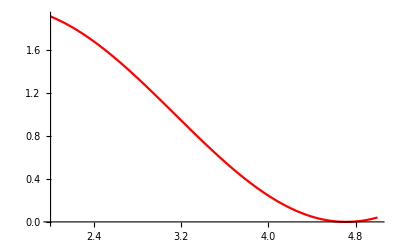

```mathematica
myPlot[Sin[x]+1,minValue->2,PlotStyle->Red]
```

### Attributes

Constant, Flat, HoldAll, HoldAllComplete, HoldFirst, HoldRest, Listable, Locked, NHoldAll,NHoldFirst, NHoldRest, NumericFunction,OneIdentity,Orderless, Protected, ReadProtected, SequenceHold, Stub, Temporary

#### Constant

Constants always have derivative zero

```mathematica
Attributes[f]={Constant}
```

{Constant}

```mathematica
D[f[x],x]
```

0

```mathematica
D[g[x],x]
```

g'[x]

```mathematica
Attributes[π]
```

{Constant,Protected,ReadProtected}

#### Flat

This is similar to giving the symbol the associative property

```mathematica
ClearAll[f]
Attributes[f]={Flat};
```

```mathematica
f[f[a,b],c]==f[a,f[b,c]]
```

True

```mathematica
g[g[a,b],c]==g[a,g[b,c]]
```

g[g[a,b],c]==g[a,g[b,c]]

#### HoldAll, HoldAllComplete, HoldFirst, HoldRest, NHoldAll,NHoldFirst, NHoldRest, SequenceHold

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

#### Listable

Listable gives you the ability to apply a function to the elements of a list when it is

```mathematica
ClearAll[f]
SetAttributes[f,Listable]
```

```mathematica
f[{a,b,c}]
```

{f[a],f[b],f[c]}

#### Orderless

This attribute is similar to commutativity

```mathematica
ClearAll[f]
SetAttributes[f,Orderless]
```

```mathematica
f[a,b]==f[b,a]
```

True

#### Protected/ReadProtected

```mathematica
ClearAll[f]
SetAttributes[f,Protected]
```

```mathematica
f=5
```

Set::wrsym: Symbol f is Protected.

5

```mathematica
Clear[f]
```

Clear::wrsym: Symbol f is Protected.

```mathematica
Remove[f]
```

Remove::rmptc: Symbol f is Protected and cannot be removed.

```mathematica
Unprotect[f]
```

{f}

```mathematica
Remove[f]
```

### Error Messages

```mathematica
Length[a+b]
```

2

```mathematica
length[x_]:=If[Head[x]===List,Length[x],Message[f::list,x]]
```

```mathematica
length::usage = "length[x] calculates the length of x only if it is a list";
length::list="The input `1` is not a List";
```

```mathematica
?length
```

```mathematica
length
```

```mathematica
f[{1,2,3}]
```

3

```mathematica
f[5]
```

f::list: The input 5 is not a List

### Exercises

Create a function that behaves like a mathematical set construct, that is it deletes duplicates and order of its elements does not matter. For example set[c,c,a,a,a,b] evaluates to set[a,b,c]

```mathematica
ClearAll[set]
```

```mathematica
Attributes[set]={Orderless}
```

{Orderless}

```mathematica
set[a,b,c,c,c,c]
```

set[a,b,c]

```mathematica
set[y___,x_,z___,x_,w___]:=set[x,y,z,w]
```

```mathematica
Union[set[a,b,c,d],set[a,g,c]]
```

set[a,b,c,d,g]